## Analysis of logged data

### Download all data

```mathematica
historyBin=Databin["ttOfD1G4"];
```

```mathematica
allData=Get@historyBin;
```

```mathematica
Length[allData]
```

109

```mathematica
Dataset[allData[[-3;;]]]
```

Dataset[<>]

### Meal Count Breakdown

```mathematica
PieChart[
ReverseSort@Counts[allData[[All,"Data","MealType"]]],
ChartLabels->Automatic
]
```

-Graphics-

### Complete Meal days

```mathematica
groupedByDate=GroupBy[allData,DateObject[Take[First[#Timestamp],3]]&,Map[#Data&]];
```

```mathematica
completeMealDays=Keys@Select[groupedByDate[[All,All,"MealType"]],ContainsAll[{"Breakfast",(*"Lunch",*)"Dinner"}]]
completeMealDays//Length
```

{Day: Wed 4 Apr 2018,Day: Thu 5 Apr 2018,Day: Sun 8 Apr 2018,Day: Sat 7 Apr 2018,Day: Tue 10 Apr 2018,Day: Fri 13 Apr 2018,Day: Wed 18 Apr 2018,Day: Sun 22 Apr 2018,Day: Mon 23 Apr 2018,Day: Tue 24 Apr 2018,Day: Wed 25 Apr 2018,Day: Thu 26 Apr 2018,Day: Fri 27 Apr 2018,Day: Sat 28 Apr 2018}

14

```mathematica
Keys[groupedByDate]//Length
```

33

I have completely logged ~42% of the days that I have logged data.
In order to improve, I can set up reminders for myself via the cloud.

```mathematica
Quantity[100*N[Length[completeMealDays]/Length[Keys[groupedByDate]]],"Percent"]
```

42.4242 %

```mathematica
TimelinePlot[
<|
"Logged"->Keys[groupedByDate],
"Complete"->completeMealDays
|>,
PlotRange->{DateObject[{2018,3,15}],Today},
(*PlotLayout->"Packed",*)
Epilog->{Red,InfiniteLine[{{#,0},{#,1}}&[Today]]}
]
```

-Graphics-

```mathematica
completeMealDayData=KeyTake[groupedByDate,completeMealDays];
```

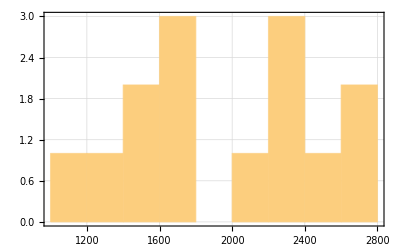

```mathematica
Histogram[
Values[Total[DeleteMissing[#[[All,"TotalCalories"]]]]&/@completeMealDayData],
{Quantity[200,"LargeCalories"]},
PlotTheme->"Detailed",
PlotRange->All
]
```

### Complete Nutrition Days (TotalCalories only?)

# of days that I got enough of each mineral

### Date Histograms

#### All Meal types

```mathematica
allTimes=(*TimeObject/@*)allData[[All,"Timestamp"]];
```

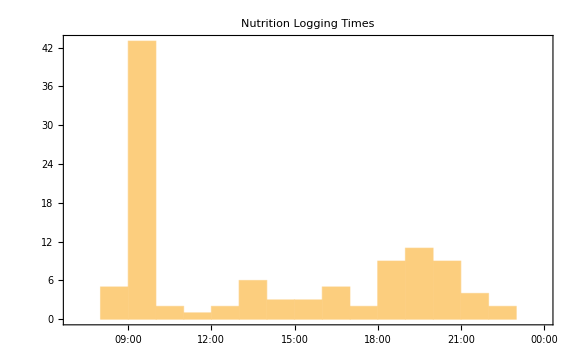

```mathematica
DateHistogram[TimeObject/@allTimes,"Hour",PlotTheme->"Detailed",ImageSize->Large,PlotLabel->"Nutrition Logging Times",PlotRange->{{TimeObject[{7,0}],TimeObject[{23,59}]},Automatic}]
```

#### Breakdown by meal type (individual plots, messier)

Breakfast happens more or less the same time each day.
There is some noise that may require some curation to clean up... Likely due to bad parsing and/or bugs that have been fixed since then.

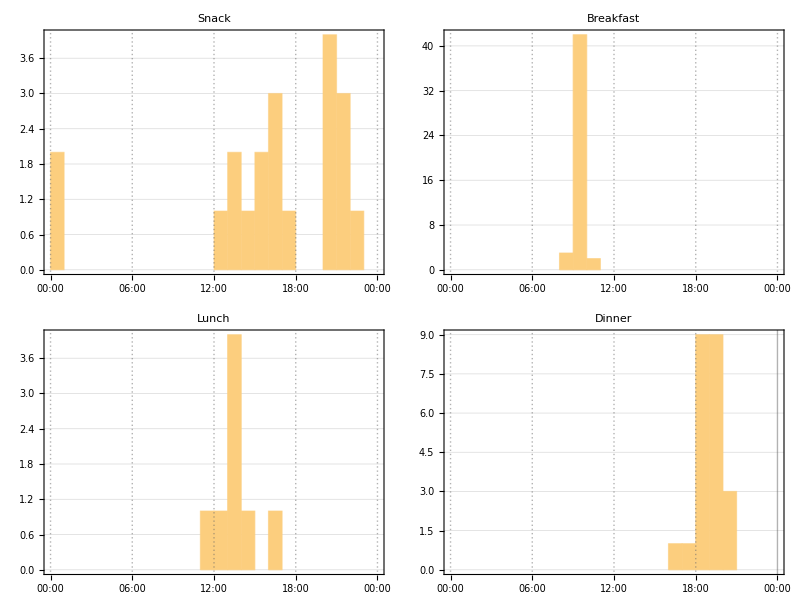

```mathematica
KeyValueMap[
DateHistogram[#2,Quantity[1,"Hours"],
DateReduction->"Day",
PlotLabel->#1,
ImageSize->Medium,
PlotTheme->"Detailed"
]&,
Merge[<|Lookup[#Data,"MealType"]->#Timestamp|>&/@allData,Map[TimeObject]]
]//Multicolumn
```

#### Breakdown by meal type (combined into one plot)

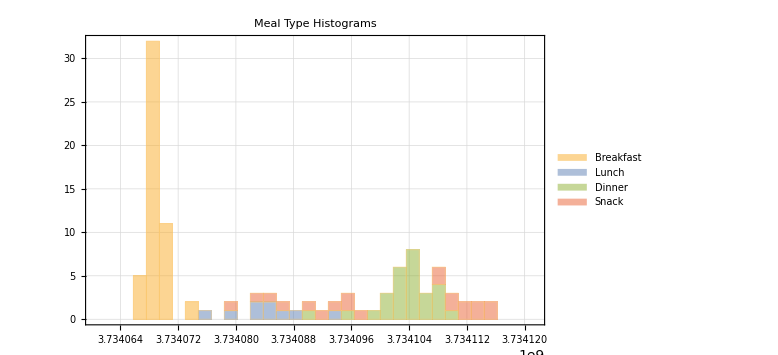

```mathematica
DateHistogram[
Merge[<|Lookup[#Data,"MealType"]->TimeObject@#Timestamp|>&/@allData,Identity]//KeyTake[{"Breakfast","Lunch","Dinner","Snack"}],
Quantity[0.5,"Hours"],
(*DateReduction->"Day",*)
ChartLegends->Automatic,
PlotTheme->"Detailed",
ImageSize->Large,
ChartLayout->"Stacked",
PlotRange->{{TimeObject[{7,0}],TimeObject[{23,59}]},Automatic},
PlotLabel->"Meal Type Histograms"
]
```

### Averaged Meal nutrition

```mathematica
gridOfRadarPlots=Function[{aggregationFunction},
KeyValueMap[
Column[
{
StringTemplate["`` (``)"][#1,aggregationFunction],
NutritionRadarPlot[#2,"NutritionTargets"-><|"TotalCalories"->Quantity[2000,"LargeCalories"]|>,ImageSize->Medium]
},
Alignment->Center
]&,
Merge[GroupBy[#,#MealType&,Total@DeleteMissing[KeyDrop[#,{"Meal","MealType"}]]&]&/@Values[completeMealDayData],Merge[#,aggregationFunction[DeleteMissing[#]/._Missing->0]&]&]//Map[KeyDrop["TotalFiber"]]//KeyDrop[{"Lunch"}]
]
]/@{Median,Mean};
```

```mathematica
Grid[gridOfRadarPlots//Transpose,Frame->All]
```

Breakfast (Median)
-Graphics- | Breakfast (Mean)
-Graphics-
Snack (Median)
-Graphics- | Snack (Mean)
-Graphics-
Dinner (Median)
-Graphics- | Dinner (Mean)
-Graphics-